```mathematica
independetvars={t,x,y,z}
```

{t,x,y,z}

```mathematica
Needs["PlotLegends`"]
Dt[x]//TraditionalForm;
metric[lineelement_,independentvars_List]:=
Block[{lenindependent,differentials,diffmatrix,metricform,varmetric,gh,sum,equation,rule,varhelp,zeros,zerorule},

(*---determine the no. of independent variables---*)
lenindependent=Length[independentvars];

(*---create the differentials corresponding to dx,dt...---*)
differentials=Map[Dt,independentvars];

(*---a mtrix of a differential products---*)
diffmatrix=Outer[Times,differentials, differentials];

(*---the general matrix form---*)
metricform=Array[gh,{lenindependent,lenindependent}];

(*---the general metric form---*)
varmetric=Variables[metricform];

(*---build a system of equations to determine the elements of the metric---*)
If[Length[metricform]==Length[diffmatrix],
sum=0;
Do[
Do[
sum=sum+metricform[[i,j]] diffmatrix[[i,j]],
{j,1,lenindependent}],
{i,1,lenindependent}],
sum=0
];

(*---construct the metric tensor---*)
If[sum===0,
Return[sum],
sum=sum-lineelement;
equation=CoefficientList[sum,differentials]==0;
rule=Solve[equation,varmetric];
metricform=metricform/.rule;
varmetric=Variables[metricform];

(*---replace the nonzero elements---*)
varhelp={};
Do[
If[Not[FreeQ[varmetric[[i]],gh]],
AppendTo[varhelp,varmetric[[i]] ]
],
{i,1,Length[varmetric]}];
zeros=Table[0,{Length[varhelp]}];
SubstRule[x_,y_]:=x->y;
zerorule=Thread[SubstRule[varhelp,zeros]];
metricform=Flatten[metricform/.zerorule,1];

(*---make the metricform symmtric---*)
metricform=Expand[(metricform+Transpose[metricform])/2]
];
metricform
];
Off[Solve::svars];
Off1[Solve:: svars];
```

```mathematica
(* Schwarzschild metric *)
```

```mathematica
ds2=(1-(2 m)/r) Dt[t]^2-(1-(2 m)/r)^-1 Dt[r]^2-r^2 Dt[θ]^2-r^2 Sin[θ]^2 Dt[ϕ]^2
```

-Dt[r]^2/(1-2/r)+(1-2/r) Dt[t]^2-r^2 Dt[θ]^2-r^2 Dt[ϕ]^2 Sin[θ]^2

```mathematica
coords={t,r,θ,ϕ};
n=Length[coords];
```

```mathematica
gμν=metric[ds2,{t,r,θ,ϕ}];
gμν//MatrixForm
```

(1-2/r | 0 | 0 | 0
0 | -r/(-2+r) | 0 | 0
0 | 0 | -r^2 | 0
0 | 0 | 0 | -r^2 Sin[θ]^2)

```mathematica
inversegμν=Simplify[Inverse[gμν]];
inversegμν//MatrixForm
```

(r/(-2+r) | 0 | 0 | 0
0 | -1+2/r | 0 | 0
0 | 0 | -1/r^2 | 0
0 | 0 | 0 | -Csc[θ]^2/r^2)

```mathematica
(* Christoffel symbols *)
```

```mathematica
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversegμν[[μ,σ]])*(D[gμν[[σ,ν]],coords[[λ]] ]+D[gμν[[σ,λ]],coords[[ν]] ]-D[gμν[[ν,λ]],coords[[σ]] ]), {σ,1,n}],{μ,1,n},{ν,1,n},{λ,1,n}] ]
```

```mathematica
listchristoffel:=Table[If[UnsameQ[christoffel[[μ,ν,λ]],0],{Style[Subsuperscript[Γ,Row[{ν-1,λ-1}],μ-1],16],"=",Style[christoffel[[μ,ν,λ]],17]}],{μ,1,n},{ν,1,n},{λ,1,ν}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listchristoffel],Null],3],TableSpacing->{2,2}]
```

Γ_10^0 | = | 1/((-2+r) r)
Γ_00^1 | = | (-2+r)/r^3
Γ_11^1 | = | 1/(2 r-r^2)
Γ_22^1 | = | 2-r
Γ_33^1 | = | -(-2+r) Sin[θ]^2
Γ_21^2 | = | 1/r
Γ_33^2 | = | -Cos[θ] Sin[θ]
Γ_31^3 | = | 1/r
Γ_32^3 | = | Cot[θ]

```mathematica
(* geodesci equations *)

geodesic:=geosdesic=Simplify[Table[-Sum[christoffel[[i,j,k]] coords[[j]]' coords[[k]]',{j,1,n},{k,1,n}],{i,1,n}]]
listgeodesic:=Table[{"d/dτ" ToString[coords[[i]]'],"=",geodesic[[i]]},{i,1,n}]
TableForm[listgeodesic,TableSpacing->{2}]
```

d/dτ t' | = | -(2 r' t')/((-2+r) r)
d/dτ r' | = | (r^2 (r')^2+(-2+r)^2 (-(t')^2+r^3 ((θ')^2+Sin[θ]^2 (ϕ')^2)))/((-2+r) r^3)
d/dτ θ' | = | -(2 r' θ')/r+Cos[θ] Sin[θ] (ϕ')^2
d/dτ ϕ' | = | -(2 (r'+r Cot[θ] θ') ϕ')/r

```mathematica
(* schwarzschild orbits *)
```

```mathematica
computeSoln[maxτi_,ivsi_,icsi_]:=Block[{ivs,ics,i,χ,tmp,soln},
ics=icsi;
ivs=Join[{χ},ivsi];
tmp=gμν;
tmp=tmp/.Table[coords[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[coords[[i]]''[τ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[τ],{i,1,n}],
Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]] [0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords,{τ,0,maxτi}];
soln]
uinvar=1;
```

```mathematica
sphslnToCartsln[soln_]:=Block[{xs,ys,zs},xs=r[τ] Sin[θ[τ]] Cos[ϕ[τ]]/.soln;
ys=r[τ] Sin[θ[τ]] Sin[ϕ[τ]]/.soln;zs=r[τ] Cos[θ[τ]]/.soln;{xs,ys,zs}]
```

```mathematica
udotu[solni_,τval_]:=Block[{xα,uα},
xα=Table[coords[[i]][τ]/.solni,{i,1,n}]//Flatten;
uα=D[xα,τ];
xα=xα/.τ->τval;
uα=uα/.τ->τval;
uα.((gμν/.Table[coords[[i]]->xα[[i]],{i,1,n}]).uα)]
```

```mathematica
coordlist[τin_]:=Table[ToString[coords[[i]]]<>" = "<>{ToString[coords[[i]][τin]/.soln//First]},{i,1,n}]
```

```mathematica
m=1;
maxτ=2000;
ivs={0,0,.088};
ics={0,6.5,π/2,1};
soln=computeSoln[maxτ,ivs,ics];
```

```mathematica
xyzsoln=sphslnToCartsln[soln];
```

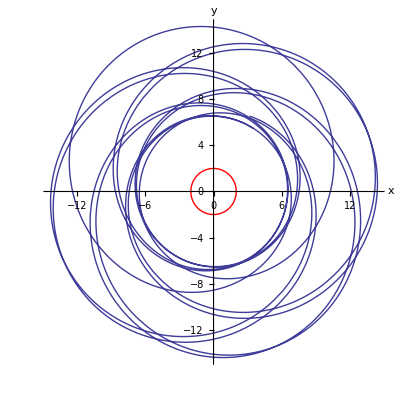

Final Coordinate:
t = 2389.72
r = 7.27271
θ = 1.5708
ϕ = 76.5173

proper time |  |  | u.u values
τ= | 0 | → | 1.
τ= | 400 | → | 1.
τ= | 800 | → | 1.
τ= | 1200 | → | 1.
τ= | 1600 | → | 1.
τ= | 2000 | → | 1.

```mathematica
horizonplot=PolarPlot[2,{θ,0,2 Pi},PlotStyle->Hue[0],DisplayFunction->Identity];
ParametricPlot[Evaluate[{xyzsoln[[1]],xyzsoln[[2]]}//Flatten],{τ,0,maxτ},AxesLabel->{x,y},DisplayFunction->Identity];
Show[%,horizonplot,DisplayFunction->$DisplayFunction]
Join[{"Final Coordinate:"},coordlist[maxτ]]//TableForm
Join[{{"proper time","","","u.u values"}},Table[{"τ=",ToString[i],"→",udotu[soln,i]},{i,0,maxτ,maxτ/5}]]//TableForm
```

```mathematica
(* Schwarzschild orbits: 3D plot *)
```

```mathematica
xyzsoln=sphslnToCartsln[computeSoln[maxτ,ivs,ics]];
sphhorizon=SphericalPlot3D[{2,EdgeForm[]},{θ,0,Pi},{ϕ,0,2 Pi},DisplayFunction->Identity];
angle=ParametricPlot3D[Evaluate[Re[xyzsoln]//Flatten],{τ,0,maxτ},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotPoints->5000];
Show[angle,sphhorizon,DisplayFunction->$DisplayFunction,PlotRange->{{-20,20},{-20,20},{-20,20}}]
```

-Graphics3D-

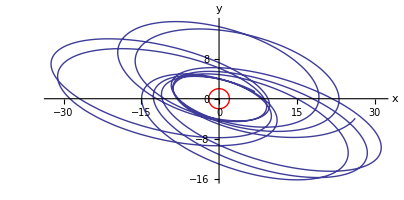

Final Coordinates:
t = 5428.87
r = 27.556
θ = 1.30022
ϕ = 62.6849

proper time |  |  | u.u values
τ= | 0 | → | 1.
τ= | 1000 | → | 1.
τ= | 2000 | → | 1.
τ= | 3000 | → | 1.
τ= | 4000 | → | 1.
τ= | 5000 | → | 1.

```mathematica
(* Kerr metric orbitals *)
m=1;
maxτ=5000;
ivs={-.08,-.035,.0359};
ics={0,10,π/4,.2};
soln=computeSoln[maxτ,ivs,ics];
xyzsoln=sphslnToCartsln[soln];
horizonplot=PolarPlot[2,{θ,0,2 Pi},PlotStyle->Hue[0],DisplayFunction->Identity];
ParametricPlot[Evaluate[{xyzsoln[[1]],xyzsoln[[2]]}//Flatten],{τ,0,maxτ},AxesLabel->{x,y},DisplayFunction->Identity];
Show[%,horizonplot,DisplayFunction->$DisplayFunction]
Join[{"Final Coordinates:"},coordlist[maxτ]]//TableForm
Join[{{"proper time","","","u.u values"}},Table[{"τ=",ToString[i],"→",udotu[soln,i]},{i,0,maxτ,maxτ/5}]]//TableForm
```

```mathematica
(* kerr metric orbitas: 3D plot *)
```

```mathematica
xyzsoln=sphslnToCartsln[computeSoln[maxτ,ivs,ics]];
sphhorizon=SphericalPlot3D[{2,EdgeForm[]},{θ,0,Pi},{ϕ,0,2 Pi},DisplayFunction->Identity];
angle=ParametricPlot3D[Evaluate[Re[xyzsoln]//Flatten],{τ,0,maxτ},AxesLabel->{x,y,z},DisplayFunction->Identity];
Show[angle,sphhorizon,DisplayFunction->$DisplayFunction]
```

-Graphics3D-

-Graphics3D-